## 3 | Quantum Approximate Optimization Algorithm (QAOA)

The Quantum Approximate Optimization Algorithm (QAOA) is a well-studied approach for solving combinatorial optimization problems.

### Combinational Optimization

The combinatorial optimization problem involves finding an optimal object from a finite set of objects. This problem can be formulated as maximizing an objective function, which is expressed as a sum of Boolean functions.

Each Boolean function C_i:{0,1}^n->{0,1} takes a n-bit string z=z_1 z_2(…z)_n as input and produces a single bit (0 or 1) as output.

For a problem with n bits and m clauses, the goal is to find a n-bit string z that maximizes the function:

C(z)=∑_(i=1)^m C_i(,z,)

Approximate optimization aims to find a near-optimal solution to this problem, which is often NP-hard. The approximate solution is an n-bit string z that closely maximizes the objective function 𝐶(z).

### Quantum Approximate Optimization Algorithm

The Quantum Approximate Optimization Algorithm (QAOA) is a well-studied approach for solving combinatorial optimization problems. First proposed by Edward Farhi as a Variational Quantum Algorithm (VQA) designed to find approximate solutions to the Max–Cut problem, and to be executable on Near–term Intermediate–Scale Quantum (NISQ) devices.

The QAOA was formulated as a variational approach that alternates between cost and mixer layers. Specifically, QAOA applies a sequence of alternating unitaries: the cost unitary U_C(γ_i) and the mixer unitary U_M(θ_i), where i denotes the layer index. The central idea is to encode the objective function of a combinatorial optimization problem into a cost Hamiltonian H_C , and then variationally optimize the parameters to search for an optimal bitstring.

The QAOA process involves the following steps:

Defining a Cost Hamiltonian H_C:
This Hamiltonian is designed such that its ground state encodes the optimal solution to the combinatorial optimization problem.

Defining a Mixer Hamiltonian H_M:
This Hamiltonian is used to explore the solution space by driving transitions between different states.

Defining the unitary gates:

U_C(γ)=ⅇ^(-ⅈ*\bt*H_C(γ)), U_M(θ)=ⅇ^(-ⅈ*\bθ*H_M(θ))

Applying the gates alternately in layers, forming the unitary:

U(γ,θ)=∏_(i=1)^N U_c(γ)U_M(θ)

Preparing an Initial State and Applying U(t,θ):
The initial state is typically a superposition of all possible states. The alternating application of  U_C and U_M evolves this state according to the chosen parameters.

Optimizing Parameters and Measuring:
Classical optimization techniques are used to adjust the parameters t and θ to maximize the expectation value of the cost Hamiltonian H_C. The measurement of the final state provides an approximate solution to the original problem.

## Max-Cut Problem

The Max–Cut problem is one of the most prominent and widely studied combinatorial optimization problems. It consists of finding a partition of the vertices of a graph into two complementary subsets in such a way that the total weight of the edges crossed by the cut is maximized.

### Formulating Max-Cut with Classical Binary Variables

Consider an undirected graph G=(V,E), where V is the set of vertices, E the set of edges, and ω_ij denotes the weight of the edge (i,j )∈E, connecting vertices i and j. The goal is to partition the graph vertices x_i for i ϵ {1,…,|V|}, into two complementary subsets labeled as  s_i ∈ {-1,1} in such a way that the total weight of the edges between vertices in different subsets is maximized.

```mathematica
g=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,4},{2,3},{3,4}},];
highlited=HighlightGraph[g,(Subgraph[g,#]&)/@Last[FindMaximumCut[g]],];cut=Show[{,highlited},];
GraphicsRow[{g,cut}]
```

-Graphics-

Considering the plain Max-Cut problem (ω_ij=1), this sumation is defined as:

C=1/2∑_(𝒾,𝒿 ∈ V) (1-s_𝒾 s_𝒿), s∈{-1,+1}

Analyzing the following cost function, we notice:

If s_i and s_j have opposite signs:
The cut contributes to the objective function because the vertices are placed in different sets. Mathematically, this happens because C_ij=1-s_𝒾 s_𝒿=1.

If s_i and s_j have same sign:
Then they remain in the same subset, meaning there is no cut and the edge does not contribute to the objective function because C_ij=1-s_𝒾 s_𝒿=0.

Use the Wolfram Language function FindMaximumCut to solve the classical Max-Cut problem:

```mathematica
FindMaximumCut[g]
```

{4,{{1,3},{2,4}}}

This follows the solution given in the first image:

```mathematica
cut
```

-Graphics-

### Formulating Max-Cut with Quantum Mechanics

To solve the Max-Cut problem on a quantum computer, we need to reformulate it in terms of quantum mechanics. Specifically, we convert the classical optimization problem into one of finding the eigenstate of a quantum Hamiltonian.

In the classical case, we represent a solution using a binary string where each vertex has an associated value s_𝒾∈{-1,1}. In the quantum case, we represent each vertex using a qubit. Since the eigenvalues of Z are also ±1, we map these classical binary variables onto the eigenvalues of the Pauli-Z operator.

Our goal now shifts from finding a binary string to identifying the highest-energy eigenstate of a quantum Hamiltonian.

To proceed, we first load the Wolfram Quantum Framework:

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

#### Hamiltonian formulation

Max-Cut Hamiltonian obtained by mapping the binary variables s_i onto Pauli-Z eigenvalues:

H_C=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Z_𝒾 Z_𝒿)

where the Z_i operator acts on the i-th qubit (node).

Represent each node as a qubit, then we have the bitstring:

x_1(…x)_n

By applying the Z_i Z_j  operators to the bitstring, we can gain insight into its behavior, which is useful for reformulating the problem:

Z_i Z_j x_0(…x)_n=(-1)^x_i(-1)^x_j x_0(…x)_n,x_i∈{0,1}

Based on this result, we switch from the classical variables s_i∈{-1,1} to x_i∈{0,1}, in order to label the two complementary subsets being cut.

Considering the initial problem, we can implement H_C using the Graph functionalities:

```mathematica
index=MapApply[List,EdgeRules[g]]/.x_Integer:>{x,x};
op𝟙=StringRepeat["I",VertexCount[g]];
sum=Total[1/2(op𝟙-StringReplacePart[op𝟙,"Z",#])&/@index]
```

(IIII-IIZZ)/2+(IIII-IZZI)/2+(IIII-ZIIZ)/2+(IIII-ZZII)/2

We’ve defined the summation and specified which qubits are coupled via Z operators. You can also write the Pauli operators manually as an String.

Next, we generate the Cost Hamiltonian QuantumOperator:

```mathematica
Hc=QuantumOperator[sum]
```

QuantumOperator[…]

#### Solution analysis

For the previous problem, we obtained the classical solution {-1,1,-1,1} or the symmetrical analogue {1,-1,1,-1} with C=4:

For the quantum case, the solution will be encoded in the resultant state or bitstring, in this case it would be read as 0101 or 1010:

### Understanding QAOA Ansatz

To implement the Max-Cut problem on a quantum computer, we start by putting the nodes in superposition. This ensures that each node (qubit) has an equal probability of being in either partition.

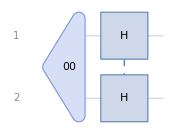

```mathematica
superposition=QuantumCircuitOperator[{"00","HH"},"Label"->"+^(⊗4)"];
superposition["Diagram",ImageSize->Small]
```

We apply a Hadamard gate (H) to each qubit, This transforms the initial state 0 of all qubits into a superposition of all possible cuts:

```mathematica
superposition["Formula"]
```

1/2 00+1/2 01+1/2 10+1/2 11

```mathematica
superposition["Probabilities"]
```

<|00→1/4,01→1/4,10→1/4,11→1/4|>

Some initial intuition comes from our first example, which involves identifying a periodic pattern, such as 0101 or 1010, within a bitstring.

To achieve this, we need to establish connections between nodes or qubits that reflect the structure of the cost Hamiltonian. For this initial idea, we can evaluate the gate sequence CNOT + RZ + CNOT.

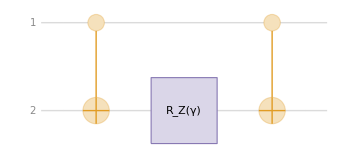

```mathematica
qcrzz=QuantumCircuitOperator[{"CNOT","RZ"[γ]->{2},"CNOT"},"Label"->"Cost"];
qcrzz["Diagram"]
```

We can verify that it distinguish the possible correct solutions from the non-periodic bitstrings in order to solve the problem:

```mathematica
qcrzz[QuantumState["++"]]["Formula"]
```

1/2 ⅇ^(-(ⅈ γ)/2)00+1/2 ⅇ^((ⅈ γ)/2)01+1/2 ⅇ^((ⅈ γ)/2)10+1/2 ⅇ^(-(ⅈ γ)/2)11

We can gain some initial insights and visualize the differences in the solution amplitudes in the following plot:

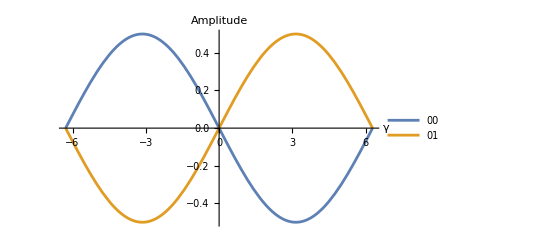

```mathematica
Plot[Evaluate[Im[Values[#]]],{γ,-2π,2π},]&@Normal[qcrzz[QuantumState["++"]]["Amplitudes"]][[;;2]]
```

The concept becomes clearer when we observe that the probabilities of regular bitstrings are minimal when the probabilities of periodic bitstrings are maximal, and vice versa:

```mathematica
qcrzz[QuantumState["++"]]["Probability"]
```

<|00→ⅇ^Im[γ]/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),01→ⅇ^(-Im[γ])/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),10→ⅇ^(-Im[γ])/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),11→ⅇ^Im[γ]/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2))|>

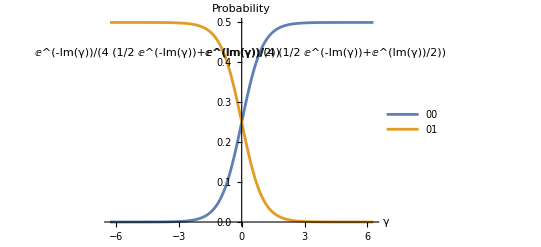

```mathematica
Plot[Evaluate[Values[#]/.Im[γ]:>γ],{γ,-2π,2π},]&@Normal[qcrzz[QuantumState["++"]]["Probability"][[;;2]]]
```

The set of gates outlined earlier is commonly referred to as an RZZ gate, which combines rotations and controlled operations:

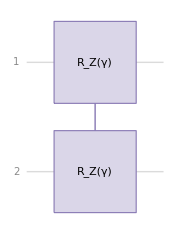

```mathematica
QuantumCircuitOperator[{{"R",γ,"ZZ"}}]["Diagram",ImageSize->Small]
```

```mathematica
QuantumCircuitOperator[{{"R", γ, "ZZ"}}]["Table"]
```

| 00 | 01 | 10 | 11
00 | ⅇ^(-(ⅈ γ)/2) | 0 | 0 | 0
01 | 0 | ⅇ^((ⅈ γ)/2) | 0 | 0
10 | 0 | 0 | ⅇ^((ⅈ γ)/2) | 0
11 | 0 | 0 | 0 | ⅇ^(-(ⅈ γ)/2)

Now that we understand this, we can apply it to every pair of qubits connected in the graph. In other words, we apply the RZZ gate to every edge in the graph. This ensures that the quantum state evolves according to the problem constraints.

The previous step does not explore all possible cuts because some amplitudes remain unchanged, so we need to mix things a little bit!

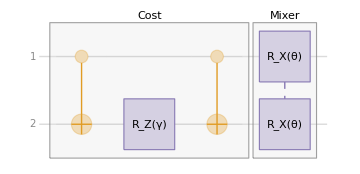

```mathematica
miniMixer=QuantumCircuitOperator[{"RX"[θ]->{1,2}},"Label"->"Mixer"];
miniqaoa=QuantumCircuitOperator[{qcrzz,miniMixer}];
miniqaoa["Diagram"]
```

Visualize the symbolic function corresponding to each possible state:

```mathematica
miniqaoa["Simplify"]["Table"]
```

| 00 | 01 | 10 | 11
00 | ⅇ^(-(ⅈ γ)/2) Cos[θ/2]^2 | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -ⅇ^(-(ⅈ γ)/2) Sin[θ/2]^2
01 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ] | ⅇ^((ⅈ γ)/2) Cos[θ/2]^2 | -ⅇ^((ⅈ γ)/2) Sin[θ/2]^2 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
10 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ] | -ⅇ^((ⅈ γ)/2) Sin[θ/2]^2 | ⅇ^((ⅈ γ)/2) Cos[θ/2]^2 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
11 | -ⅇ^(-(ⅈ γ)/2) Sin[θ/2]^2 | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | ⅇ^(-(ⅈ γ)/2) Cos[θ/2]^2

Considering the initial state preparation, we recover a mini-QAOA:

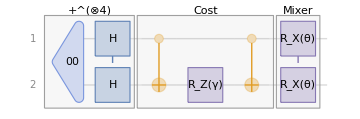

```mathematica
miniqaoa[superposition]["Diagram"]
```

The increased expressibility of the resulting state from this ansatz, as compared to previous circuits, comes from the final mixing performed by the mixing layer of gates:

```mathematica
miniqaoa[superposition]["Simplify"]["Table"]
```

| 1
00 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]
01 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
10 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
11 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]

From the following plot, we can observe how the probabilities for regular and periodic bitstrings oscillate, similar to the previous plots. The new parameter θ does not interfere with this behavior; instead, it expands the parameter space, providing additional expressibility to our ansatz:

```mathematica
Plot3D[Evaluate[ComplexExpand@Values[#]],{γ,-2π,2π},{θ,-π,π},PlotLegends->Keys[#],AxesLabel->{"γ","θ","Probability"}]&@Normal[miniqaoa[superposition]["Probabilities"][[;;2]]]
```

-Graphics3D-

### Step–by–Step: 4-Edge Graph Example

Find the Max-Cut for the following graph:

```mathematica
g=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,4},{2,3},{3,4}},]
```

-Graphics-

Implement the Cost Hamiltonian:

```mathematica
Hc=QuantumOperator[1/2("IIII"-"ZZII")+1/2("IIII"-"IZZI")+1/2("IIII"-"IIZZ")+1/2("IIII"-"ZIIZ")]
```

QuantumOperator[…]

Initial state preparation for superposition:

```mathematica
stateprep=QuantumCircuitOperator[{"0000","H"->{1,2,3,4}},"Label"->"+^(⊗4)"];
```

We can use Wolfram Mathematica's Graph functionalities to establish connections between qubits within the Cost-Circuit:

```mathematica
qpairs=List@@@EdgeList[g]
```

{{1,2},{1,4},{2,3},{3,4}}

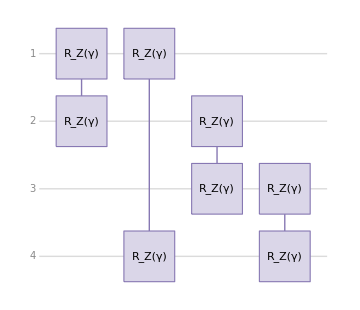

```mathematica
qcost=QuantumCircuitOperator[Map[{"R",γ,"ZZ"}->#&,qpairs],"Parameters"->{γ},"Label"->"U_Cost"];
qcost["Diagram"]
```

This layer of gates actually corresponds to the operator generated by the Cost Hamiltonian we defined earlier:

H_c=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Z_𝒾 Z_𝒿)->U_Cost=∏_(𝒾,𝒿) ⅇ^(-(ⅈ t)/2*(𝟙-Z_𝒾 Z_𝒿))

```mathematica
qcost==(ⅇ^(-2 ⅈ t)*ⅇ^(ⅈ*t*Hc))
```

True

To ensure full exploration, we need a mixer Hamiltonian that allows transitions between different states:

H_M=∑_(𝒿 ∈ V) X_j->U_Mixer=∏_(𝒿=1)^n ⅇ^(-ⅈθ*X_𝒿)

```mathematica
mixer=QuantumCircuitOperator[{"RX"[θ] -> VertexList[g]}, "Label" -> "U_Mixer","Parameters"->{θ}];
```

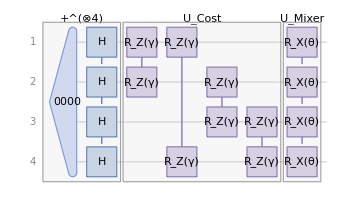

```mathematica
qaoa=QuantumCircuitOperator[{stateprep,qcost,mixer},"Parameters"->{θ,γ}];
qaoa["Diagram"]
```

Define the variational states to calculate the Cost function:

```mathematica
ϕ=qaoa[];ϕ=SuperDagger[ϕ];
```

```mathematica
costfunction=FullSimplify[ϕ@Hc@ϕ,{θ,γ}∈Reals]["Scalar"]
```

2-4 Cos[γ] Cos[θ] Sin[γ] Sin[θ]

Let's try out the NMaximize optimizer:

```mathematica
qaoaOpt=NMaximize[costfunction,{θ,γ}]
```

{3.,{θ→-0.785398,γ→0.785398}}

Visualize the most probable solutions:

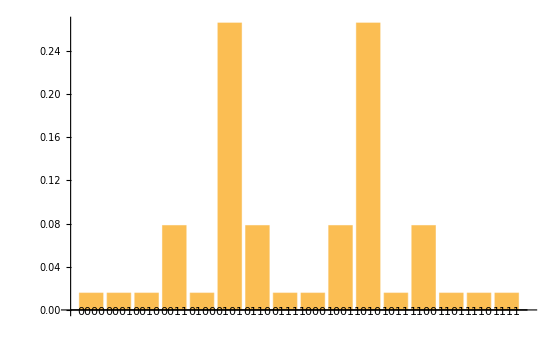

```mathematica
qaoa[<|Last@qaoaOpt|>][]["ProbabilityPlot"]
```

We obtain an initial approximate result. We detect that the solutions with higher probability are the correct answers. However, the exact solution for this problem is C=4, so we haven't reached the desired outcome yet.

We can enhance the precision of our solution by increasing the number of QAOA layers. This is easy to do since we can use QuantumCircuitOperator with the previous circuit but replacing the parameters:

```mathematica
twolayers=QuantumCircuitOperator[{stateprep,qcost[γ1],mixer[θ1]->{1,2,3,4},qcost[γ2],mixer[θ2]->{1,2,3,4}},"Parameters"->{γ1,γ2,θ1,θ2}];
```

We can utilize the Parameters option from the Wolfram Quantum Framework to re-name the gate parameters, allowing us to distinguish one layer from another.

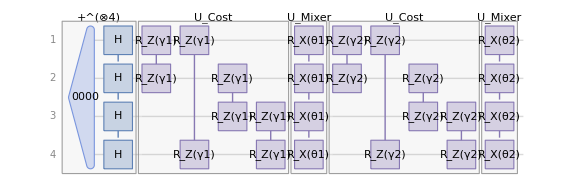

```mathematica
twolayers["Diagram",ImageSize->Large]
```

Implement the cost function:

```mathematica
Φ=twolayers[];Φ=SuperDagger[Φ];
```

```mathematica
costFunction=FullSimplify[Φ@Hc@Φ,{γ1,γ2,θ1,θ2}∈ Reals]["Scalar"]
```

1/4 (8-Cos[2γ1-2 θ1]+Cos[2 (γ1+θ1)]+4 (Cos[γ1+2 γ2]-2 Cos[γ2] Cos[γ1+γ2] Cos[2 θ2]) Sin[γ1] Sin[2 θ1]-2 ((Cos[γ1-2 γ2]+3 Cos[γ1+2 γ2]) Cos[2 θ1] Sin[γ1]+2 Cos[γ1]^2 Sin[2 γ2]) Sin[2 θ2])

Optimimize:

```mathematica
result=NMaximize[costFunction,{θ1,θ2,γ1,γ2}]
```

{4.,{θ1→1.11852,θ2→0.904557,γ1→-0.904557,γ2→-1.11852}}

Now, we obtain the exact result.

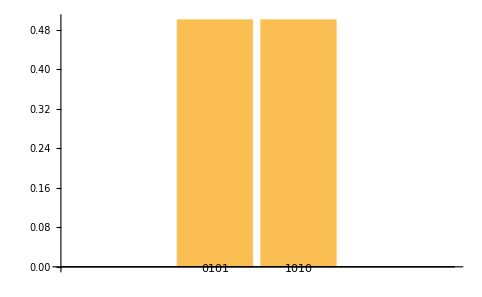

```mathematica
twolayers[<|Last@result|>][]["ProbabilityPlot"]
```

This solution represents the cut shown in the first image of this section:

```mathematica
Replace[cut,-1->0,{9}]
```

-Graphics-

We can see that 0101 is represented in this image by reading the nodes according to their indexing order. A symmetric solution can be obtained by renaming the nodes to 1010. Ultimately, what matters most is that the qubits are divided into two distinct sets, labeled as 0 or 1.

### Example: 5-Edge Graph

With a clear understanding of each step involved in solving the Max-Cut problem using QAOA, we are now ready to proceed with the direct implementation of the solution.

Find the Max-Cut for the following graph:

```mathematica
g2=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,3},{2,3},{2,4},{3,5},{4,5}},]
```

-Graphics-

In this more challenging example, we will generate the Hamiltonian programmatically instead of writing it explicitly:

```mathematica
index2=MapApply[List,EdgeRules[g2]]/.x_Integer:>{x,x};
op𝟙2=StringRepeat["I",VertexCount[g2]];
sum2=Total[1/2(op𝟙2-StringReplacePart[op𝟙2,"Z",#])&/@index2]
```

(IIIII-IIIZZ)/2+(IIIII-IIZIZ)/2+(IIIII-IZIZI)/2+(IIIII-IZZII)/2+(IIIII-ZIZII)/2+(IIIII-ZZIII)/2

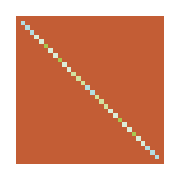

```mathematica
Hc2=QuantumOperator[sum2];
ArrayPlot[Hc2["Matrix"],ColorFunction->"IslandColors",ImageSize->Small]
```

Implement directly the QAOA circuit using the Graph functionalities:

```mathematica
qaoa2=QuantumCircuitOperator[{
"0"->VertexList[g2],
"H"->VertexList[g2],
Sequence@@Map[{"R",γ,"ZZ"}->#&,List@@@EdgeList[g2]],
"RX"[θ]->VertexList[g2]
},
"Label"->None,"Parameters"->{θ,γ}];
```

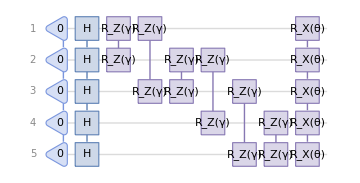

```mathematica
qaoa2["Diagram"]
```

Implement the symbolic cost function using the Cost Hamiltonian and the resulting parametrized state from the previous circuit:

```mathematica
ϕ2=qaoa2[];ϕ2=SuperDagger[ϕ2];
```

```mathematica
costfunction2=FullSimplify[ϕ2@Hc2@ϕ2,{γ,θ}∈Reals]["Scalar"]
```

1/32 (95+4 Cos[3 γ]+Cos[4 γ]+4 Cos[γ] (-1+4 Cos[2 θ] Sin[γ]^2)+2 Cos[2 θ] Sin[2 γ]^2-24 Cos[θ] (Sin[γ]+2 Sin[2 γ]+Sin[3 γ]) Sin[θ])

Use NMaximize for the optimization:

```mathematica
result2=NMaximize[costfunction2,{θ,γ}]
```

{4.30338,{θ→-35.2538,γ→-2.23284×10^27}}

We obtain multiple possible solutions; however, with just a single QAOA layer, we observe four solutions with higher probability:

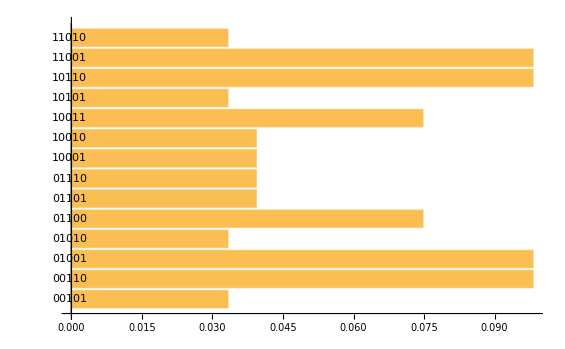

```mathematica
(qaoa2 @@ Values[Last[result2]])["ProbabilityPlot", BarOrigin -> Left,"Range"->{.02,1}]
```

Solve it clasically:

```mathematica
FindMaximumCut[g2]
```

{5,{{2,5},{1,3,4}}}

The quantum algorithm does not achieve the maximum value compared to the classical solution, but we can analyze the four most probable solutions indicated by the ProbabilityPlot:

```mathematica
ReverseSortBy[Normal[(qaoa2 @@ Values[Last[result2]])["Probabilities"]],#[[2]]&][[;;4]]
```

{10110→0.0982091,00110→0.0982091,11001→0.0982091,01001→0.0982091}

Following the labels in the vertex, the solution 10110 is the one found by the classical method. The following diagram corresponds to this solution:

```mathematica
maxcut2=HighlightGraph[g2,(Subgraph[g2,#1]&)/@Last[FindMaximumCut[g2]],];cut2=Show[{maxcut2,},];
GraphicsRow[{g2,cut2},ImageSize->Large]
```

-Graphics-

### Example: 6-Edge Graph

Find the Max-Cut for the following graph:

```mathematica
g3=Graph[Range[5],UndirectedEdge@@@{{1,2},{1,3},{2,3},{2,4},{3,5},{4,5},{4,6}},GraphStyle->"NameLabeled",EdgeStyle->Directive[Black,Thick],ImageSize->Medium]
```

-Graphics-

In this more challenging example, we have a graph with six nodes, which results in a much larger cost Hamiltonian:

```mathematica
index3=MapApply[List,EdgeRules[g3]]/.x_Integer:>{x,x};
op𝟙3=StringRepeat["I",VertexCount[g3]];
sum3=Total[1/2(op𝟙3-StringReplacePart[op𝟙3,"Z",#])&/@index3]
```

(IIIIII-IIIZIZ)/2+(IIIIII-IIIZZI)/2+(IIIIII-IIZIZI)/2+(IIIIII-IZIZII)/2+(IIIIII-IZZIII)/2+(IIIIII-ZIZIII)/2+(IIIIII-ZZIIII)/2

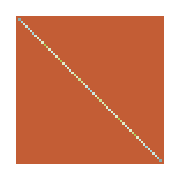

```mathematica
Hc3=QuantumOperator[sum3];
ArrayPlot[Hc3["Matrix"],ColorFunction->"IslandColors",ImageSize->Small]
```

Implement directly the QAOA circuit using the Graph functionalities:

```mathematica
qaoa3=QuantumCircuitOperator[{
"0"->VertexList[g3],
"H"->VertexList[g3],
Sequence@@Map[{"R",γ,"ZZ"}->#&,List@@@EdgeList[g3]],
"RX"[θ]->VertexList[g3]
},
"Label"->None,"Parameters"->{θ,γ}];
```

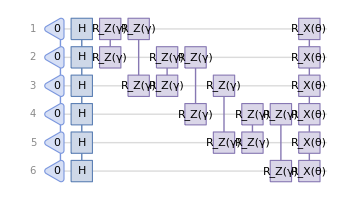

```mathematica
qaoa3["Diagram"]
```

Implement the symbolic cost function using the Cost Hamiltonian and the resulting parametrized state from the previous circuit:

```mathematica
ϕ3=qaoa3[];ϕ3=SuperDagger[ϕ3];
```

```mathematica
costfunction3="Scalar"//ϕ3@Hc3@ϕ3//ComplexExpand//Simplify
```

1/64 (222-8 Cos[γ]+8 Cos[3 γ]+2 Cos[4 γ]-22 Cos[γ-2 θ]-22 Cos[3 γ-2 θ]-Cos[4 γ-2 θ]-16 Cos[2 (γ-θ)]+2 Cos[2 θ]+16 Cos[2 (γ+θ)]-Cos[2 (2 γ+θ)]+30 Cos[γ+2 θ]+14 Cos[3 γ+2 θ])

Use NMaximize for the optimization:

```mathematica
result3=NMaximize[costfunction3,{θ,γ}]
```

{4.80604,{θ→-27.5566,γ→-32.0652}}

We obtain multiple possible solutions; however, with just a single QAOA layer, we observe four solutions with higher probability:

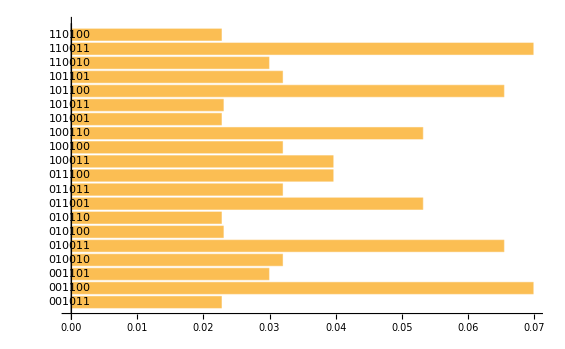

```mathematica
(qaoa3@@ Values[Last[result3]])["ProbabilityPlot", BarOrigin -> Left,"Range"->{.02,1}]
```

Solve it clasically:

```mathematica
FindMaximumCut[g3]
```

{6,{{2,5,6},{1,3,4}}}

The quantum algorithm does not achieve the maximum value compared to the classical solution, but we can analyze the four most probable solutions indicated by the ProbabilityPlot:

```mathematica
ReverseSortBy[Normal[(qaoa3 @@ Values[Last[result3]])["Probabilities"]],#[[2]]&][[;;4]]
```

{110011→0.0699094,001100→0.0699094,101100→0.0654777,010011→0.0654777}

Following the labels in the vertex, the solution 010011 is the one found by the classical method. The following diagram corresponds to this solution:

```mathematica
maxcut3=HighlightGraph[g3,(Subgraph[g3,#1]&)/@Last[FindMaximumCut[g3]],VertexLabels->];cut3=Show[{maxcut3,},];
GraphicsColumn[{g3,cut3},ImageSize->Medium]
```

-Graphics-

## QAOA-in-QAOA for Maxcut

To tackle large graphs, we use a method called QAOA-in-QAOA, inspired by the Divide and Conquer algorithm.

Here’s the idea:

First, we partition the graph into smaller subgraphs.

Next, we solve a mini-QAOA on each subgraph and combine the solutions.

Then, to correct any possible issue with the solutions between the subgraphs, we treat each subgraph as a node in a new coarse-grained graph.

Finally, we apply QAOA again to this higher-level graph and correct the final solution.

This process is recursive and scalable, making it suitable for large problem instances.

Now let’s see how the Wolfram Quantum Framework enables us to symbolically model and analyze this algorithm. Given the following graph:

```mathematica
𝓍1=UndirectedEdge@@@{{1,2},{2,3},{3,4},{2,4},{1,3}};
𝓍2=UndirectedEdge@@@(4+{{1,2},{2,3},{3,4},{1,4},{2,4},{1,3}});
𝓍3=UndirectedEdge@@@(8+{{1,2},{2,3},{3,1}});
𝓍4=UndirectedEdge@@@(11+{{1,2}});
connection=UndirectedEdge@@@{{4,11},{10,7},{9,12},{13,5},{3,7},{1,8}};
edges={𝓍1,𝓍2,𝓍3,𝓍4};
fullEdges=Flatten[{{𝓍4,𝓍2,𝓍1,𝓍3},connection}];
g=Graph[fullEdges,PlotTheme->"NameLabeled",EdgeWeight->Thread[fullEdges->1]]
```

-Graphics-

Given the following partition:

```mathematica
subgraphs=Graph[#,EdgeWeight->Thread[Rule[#,1]],]&/@edges;
gsub=HighlightGraph[fullEdges,subgraphs,]
```

-Graphics-

### Divide (Subgraphs)

We load the Hamiltonian for each minigraph:

```mathematica
subweights=<|Thread[List@@@EdgeList[#]->PropertyValue[#,EdgeWeight]]|>&/@subgraphs;
subHc=Total[Table[1/2#[i]*(QuantumOperator["I",i]-QuantumOperator["Z",i]),{i,Keys@#}]]&/@subweights
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

We then construct symbolic QAOA circuits, with qubit indices mapping directly to graph nodes:

```mathematica
subQAOA=QuantumCircuitOperator[{
"+"->VertexList[#1],
Sequence@@({"R",t,"ZZ"}->#1&)/@List@@@EdgeList[#1],
"RX"[θ]->VertexList[#1]
},
"Label"->None,"Parameters"->{θ,t}]&/@subgraphs;
```

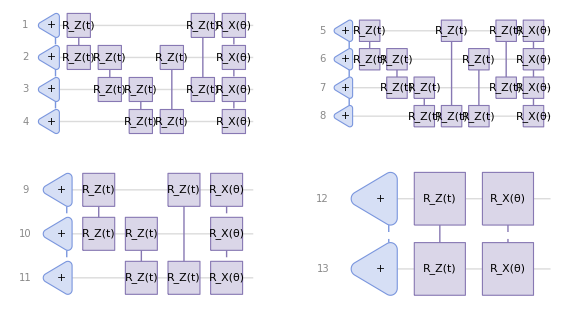

```mathematica
GraphicsGrid[Partition[#["Diagram","ShowEmptyWires"->False]&/@subQAOA,2],ImageSize->Large]
```

After simulating the states, we can observe how the symbolic computation can give insights about cost functions for each subgraph. We can visualize the parameter space using contour plots, giving us deep insight into the optimization behavior.

```mathematica
QAOAstates=QuantumOperator[#]["State"]&/@subQAOA;
```

```mathematica
subcost=Module[{ket,bra,hc},ket=#1⟦2⟧["StateVector"];bra=SuperDagger[#1⟦2⟧]["StateVector"];hc=#1⟦1⟧["Matrix"];(bra.hc.ket)//ComplexExpand//FullSimplify]&/@Thread[{subHc,QAOAstates}];
```

```mathematica
contours=ContourPlot[#,{θ,-π,π},{t,-π,π},Contours->10,ImageSize->Small]&/@subcost;
```

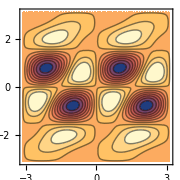
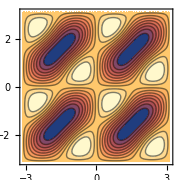
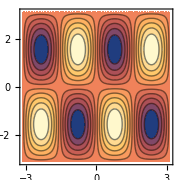
-Graphics- | -Graphics-
1/16 (-2 sin(2 θ) (3 sin(t)+4 sin(2 t)+3 sin(3 t))+4 cos(t) (2 cos(2 θ) sin^2(t) (cos(t)+2)-1)+4 cos(3 t)+cos(4 t)+39) | 
-Graphics- | -Graphics-
3/8 (-8 sin(2 θ) sin(t) cos^2(t)+2 cos(2 θ) sin^2(2 t)+cos(4 t)+7) | 
-Graphics- | -Graphics-
3/8 (-2 sin(2 θ) sin(2 t)+2 cos(2 θ) sin^2(t)+cos(2 t)+3) | 
-Graphics- | -Graphics-
1/2-sin(θ) cos(θ) sin(t) |

```mathematica
sg=Subgraph[gsub,#,ImageSize->Small]&/@{Range[4],Range[5,8],{9,10,11},{12,13}};
minigrids=Grid[{{#[[1]],#[[2]]},{Text[#[[3]],FormatType->TraditionalForm],SpanFromLeft}},Frame->All,Background->{White,{None,Lighter[Yellow,.9]}},ItemStyle->#[[4]]]&/@Thread[{sg,contours,subcost,{8,12,12,12}}];
Grid[List/@minigrids,Frame->All,BaselinePosition->Baseline,Alignment->Top,Background->Lighter[Blend[{Blue,Green}],.8]]
```

After just a single QAOA layer, we already discover useful solutions:

```mathematica
subres=NMaximize[#,{θ,t}]&/@subcost;
```

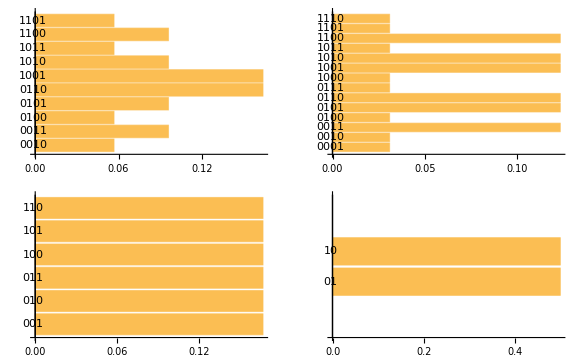

```mathematica
result=(#1⟦1⟧@@Values[Last[#1⟦2⟧]]&)/@Thread[{subQAOA,subres}];
GraphicsGrid[Partition[#["ProbabilityPlot", ]&/@result,2],ImageSize->Large]
```

Each minigraph contributes to a partial solution, illustrated by colored nodes yellow and red:

```mathematica
states=Keys@ReverseSortBy[#["Probabilities"],#[[2]]]&/@result;
groups=Map[states⟦Sequence@@##1⟧⟦1⟧&,{{1,2},{2,6},{3,1},{4,1}}];
solution=Flatten[Thread/@Thread[(First[#1["Order"]]&)/@subQAOA->groups]];
minig=Graph[g,];incompleteHigh=HighlightGraph[minig,];
GraphicsRow[{gsub,incompleteHigh},ImageSize->Full]
```

-Graphics-

### Conquer (Big graph)

In the Conquer phase, we construct a new graph where each node represents a subgraph, and the edges are based on their prior connections:

```mathematica
as=<|solution|>;
bigEdges=Complement[EdgeList[g],Flatten[EdgeList/@Map[Subgraph[g,#]&,edges]]];
smallToBig=Flatten[Thread/@Thread[VertexList/@{𝓍1,𝓍2,𝓍3,𝓍4}->Range[4]]];
bigedges=EdgeList[bigEdges]/.z:UndirectedEdge[x_,y_]:>Rule[z/.smallToBig,(-1)^as[x]*(-1)^as[y]]//Merge[#,Total]&//Normal;
g2=Graph[Reverse@#[[All,1]],EdgeWeight->#,EdgeLabels->"EdgeWeight",EdgeLabelStyle->20,PlotTheme->"NameLabeled",VertexStyle->{1 -> Hue[0,0.57,0.78,0.4], 2 ->Hue[0.15,0.82,0.87,0.4],3->Hue[0.75,0.5,0.66,0.4],4->Hue[0.05,0.62,0.87,0.6]},ImageSize->Medium]&@bigedges;
ggg=Show[{Graphics[{
Hue[0.15,0.82,0.87,0.4],Disk[{1.7,0.5},0.8],
Hue[0,0.57,0.78,0.4],Disk[{0.45,1.8},{0.8,1}],
Hue[0.75,0.5,0.66,0.4],Disk[{2.43,2.5},0.75],
Hue[0.05,0.62,0.87,0.6],Disk[{3.65,1.4},{0.3,1}]
}],incompleteHigh
}];
GraphicsRow[{ggg,g2},ImageSize->10^2.9]
```

-Graphics-

We then assign weights based on inter-subgraph interactions and repeat the QAOA process at this higher level:

```mathematica
subweights2=<|Thread[List@@@EdgeList[#]->(1-PropertyValue[#,EdgeWeight])/2]|>&@g2;
```

```mathematica
subHc2=Total[Table[1/2#[i]*(QuantumOperator["I",i]-QuantumOperator["Z",i]),{i,Keys@#}]]&@subweights2;
```

```mathematica
subQAOA2=QuantumCircuitOperator[{
"+"->VertexList[#1],
Sequence@@({"R",t,"ZZ"}->#1&)/@List@@@EdgeList[#1],
"RX"[θ]->VertexList[#1]
},
"Label"->None,"Parameters"->{θ,t}]&@g2
```

QuantumCircuitOperator[…]

```mathematica
QAOAstates2=QuantumOperator[#]["State"]&@subQAOA2;
subcost2=("Scalar"//SuperDagger[QAOAstates2]@subHc2["State"]@QAOAstates2)//ComplexExpand//Simplify
```

1/32 (22-Cos[t]+Cos[3 t]+2 Cos[4 t]-2 Cos[t-2 θ]-3 Cos[3 t-2 θ]-Cos[4 t-2 θ]-Cos[2 (t-θ)]+2 Cos[2 θ]+Cos[2 (t+θ)]-Cos[2 (2 t+θ)]+3 Cos[t+2 θ]+2 Cos[3 t+2 θ])

```mathematica
subres2=NMaximize[subcost2,{θ,t}];
```

Finally, we observe the resulting probability distribution and solve the MaxCut problem for the higher-level graph:

```mathematica
result2=subQAOA2["State"][<| Last[subres2]|>];
```

```mathematica
probplot=result2["ProbabilityPlot", ];
groups2=Part[Keys@ReverseSortBy[#["Probabilities"],#[[2]]],2][[1]]&@result2;
solution2=Flatten[Thread/@Thread[First[#["Order"]]&@subQAOA2->groups2]];
grouped2=HighlightGraph[g2,Map[Subgraph[g,#]&,GatherBy[solution2,Last][[All,All,1]]],];
GraphicsRow[{probplot,grouped2},ImageSize->Large]
```

-Graphics-

In the final step, we take the subgraphs that are yellow nodes in the higher level graph and flip their node values. For instance, in some subgraphs, yellow nodes may become red, as the global optimization balances local and global constraints.

```mathematica
flip=Keys[Select[solution2,MatchQ[#,Rule[_,1]]&]];
newsolution=#->1-as[#]&/@Keys[Select[smallToBig,MatchQ[#,Rule[_,Alternatives@@flip]]&]];
finalsolution=Normal[Association[Join@@{solution,newsolution}]];
finalsol=HighlightGraph[g,Map[Subgraph[g,#]&,GatherBy[finalsolution,Last][[All,All,1]]],]
```

-Graphics-